```mathematica
data=Import["D:\\Mod\\temperature.xlsx"];
```

```mathematica
TemperatureCurve=Table[{data[[1]][[i]][[1]],data[[1]][[i]][[2]]},{i,3,1647}];
```

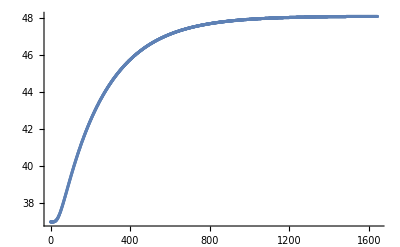

```mathematica
ListPlot[TemperatureCurve,PlotRange->All]
```

```mathematica
stage1=Table[{data[[1]][[i]][[1]],data[[1]][[i]][[2]]},{i,3,48}];
```

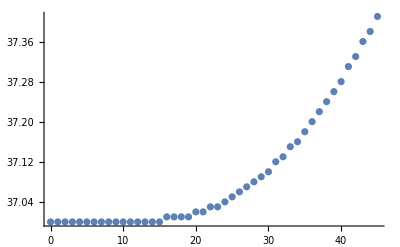

```mathematica
ListPlot[stage1,PlotRange->All]
```

```mathematica
Length[stage1]
```

56

```mathematica
data[[1]][[18]]
```

{15.,37.}

```mathematica
w=Table[stage1[[i]][[2]], {i, 18, Length[stage1]}];
```

```mathematica
FindFit[w,a+b*Exp[c*x+d],{a,b,c,d},x,MaxIterations->Infinity]
```

{a→36.83,b→74.6792,c→0.0460553,d→-6.21516}

```mathematica
zzzz=Table[{i-3,36.83+74.6792*Exp[0.0460553*(i-17)-6.21516]},{i,18,48}];
```

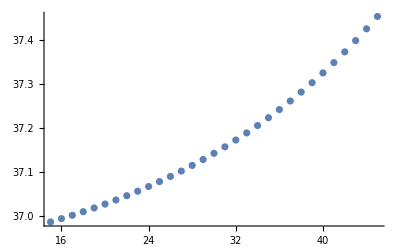

```mathematica
ListPlot[zzzz]
```

```mathematica
zzzz[[41]]
```

{55,37.8164}

```mathematica
sub[[41]]
```

{55.,37.71}

```mathematica
sub=Table[{data[[1]][[i]][[1]],data[[1]][[i]][[2]]},{i,18,48}];
```

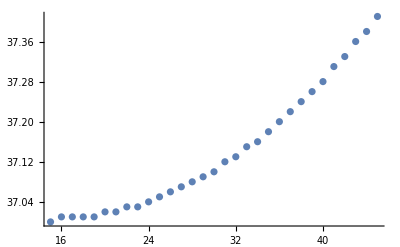

```mathematica
ListPlot[sub]
```

```mathematica
za=Table[{i,sub[[i]][[2]]-zzzz[[i]][[2]]},{i,1,31}];
```

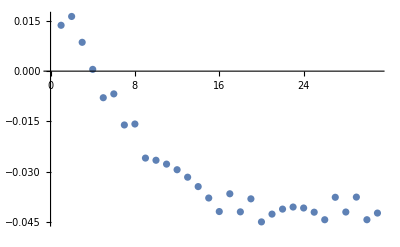

```mathematica
ListPlot[za]
```

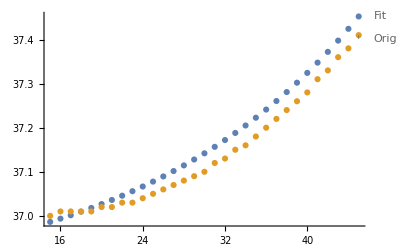

```mathematica
ListPlot[{zzzz,sub},PlotLabels->{"Fit","Orig"}]
```

```mathematica
data[[1]][[49]]
```

{ ,37.44}

```mathematica
ggg=MovingAverage[TemperatureCurve,3];
```

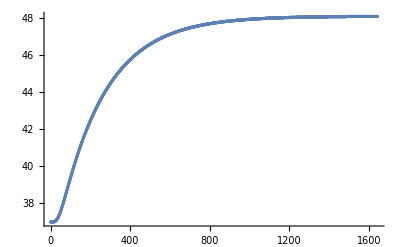

```mathematica
ListPlot[ggg,PlotRange->All]
```

```mathematica
FindFit[ggg,a+b*Exp[c*x+d],{a,b,c,d},x]
```

{a→46.2501,b→116138.,c→-141.598,d→-3.47583×10^6}

```mathematica
48.08-37
```

11.08

```mathematica
11.08/2
```

5.54

```mathematica
48.08-5.54
```

42.54

```mathematica
5.54/2
```

2.77

```mathematica
48.08-2.77
```

45.31

```mathematica
2.77/2
```

1.385

```mathematica
48.08-1.385
```

46.695

```mathematica
1.385/2
```

0.6925

```mathematica
48.08-0.6925
```

47.3875

```mathematica
0.6925/2
```

0.34625

```mathematica
48.08-0.34625
```

47.7338

```mathematica
0.34625/2
```

0.173125

```mathematica
48.08-0.173125
```

47.9069

```mathematica
0.173125/2
```

0.0865625

```mathematica
48.08-0.0865625
```

47.9934

```mathematica
0.0865625/2
```

0.0432813

```mathematica
48.08-0.04328125
```

48.0367

```mathematica
0.04328125/2
```

0.0216406

```mathematica
48.08-0.021640625
```

48.0584

```mathematica
{42.54,204}
```

```mathematica
{45.31,362}
```

```mathematica
{46.695,519}
```

```mathematica
{47.3875,675}
{47.7338,829}
```

```mathematica
{47.9069,973}
{47.9934375,1127}
{48.0367,1264}
{48.0584,1385}
```

```mathematica
204-158
```

46

```mathematica
362-204
```

158

```mathematica
519-362
```

157

```mathematica
675-519
```

156

```mathematica
829-675
```

154

```mathematica
973-829
```

144

```mathematica
1127-973
```

154

```mathematica
1264-1127
```

137

```mathematica
1385-1264
```

121

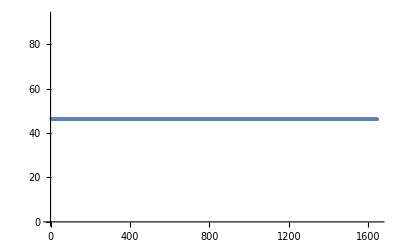

```mathematica
ggggg=Table[{i,46.2501+116138*Exp[-141.598*i-3.47583*10^6]},{i,3,1646}];
ListPlot[ggggg]
```

```mathematica
fg=Table[{i,48.08-11.08*Exp[-Log[2]*i/158]},{i,0,1644}];
```

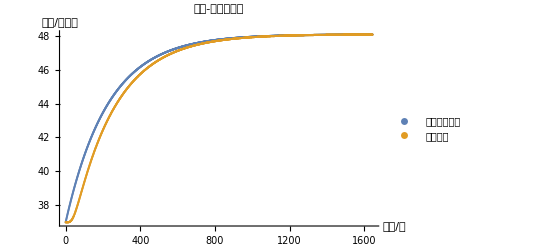

```mathematica
ListPlot[{fg,TemperatureCurve},PlotRange->All,PlotLabel->"温度-时间曲线图",PlotLegends->{"模型拟合数据","实测数据"},AxesLabel->{"时间/秒","温度/摄氏度"}]
```

```mathematica
fg1=Table[{i,48.08-11.08*Exp[-Log[2]*i/158]},{i,0,1644}];
```

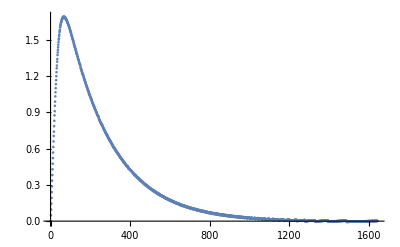

```mathematica
hhh=Table[fg[[i]][[2]]-TemperatureCurve[[i]][[2]],{i,1,1643}];
ListPlot[hhh]
```

```mathematica
FindFit[hhh,a*Exp[-b*x]+c*Exp[-d*x],{a,b,c,d},x,Method->"LevenbergMarquardt"]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a→0.830707,b→0.00314749,c→0.830763,d→0.00314749}

```mathematica
N[-Log[2]/158]
```

-0.00438701

```mathematica
(*air heat conduct coefficient:0.026*)
(*air heat capacity ratio:1000*)
(*air density:1.29*)
```

```mathematica
N[-Log[2]/158]
```

-0.00438701

```mathematica
1.29*0.026/1000
```

0.00003354

```mathematica
k=0.028/(1005*1.18)*10^6
```

23.6108

```mathematica
k0=0.082/(1377*300)*10^6
```

0.198499

```mathematica
k1=0.37/(862*2100)*10^6
```

0.204397

```mathematica
k2=0.045/(1726*74.2)*10^6
```

0.351373

```mathematica
k3=0.028/(1005*1.18)*10^6
```

23.6108

```mathematica
equ=D[u[x,t],{x,2}]-k*D[u[x,t],{t,1}]==0
```

-u^(0,1)[x,t]+u^(2,0)[x,t]==0

```mathematica
rlt=NDSolve[{D[zz[x,t],t]==k*D[zz[x,t],x,x],zz[0,t]==75,zz[x,0]==37},zz,{t,0,5},{x,0,5}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

{{zz→InterpolatingFunction[{{0., 5.}, {0., 5.}}, <>]}}

```mathematica
Plot3D[Evaluate[zz[x,t]/.%],{t,0,5},{x,0,5}, PlotRange->All]
```

-Graphics3D-

```mathematica
cc=rlt[[1]][[1]][[2]]
```

InterpolatingFunction[{{0., 10.}, {0., 10.}}, <>]

```mathematica
cc
```

InterpolatingFunction[{{0., 10.}, {0., 10.}}, <>]

44.7126

```mathematica
Plot3D[cc[x,t],{x,0,10},{t,0,10}]
```

-Graphics3D-

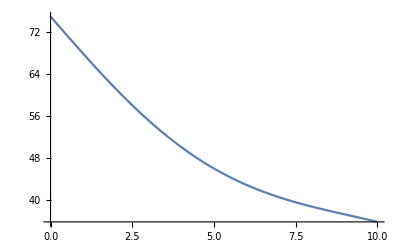

```mathematica
Plot[cc[x,10],{x,0,10},PlotRange->All]
```

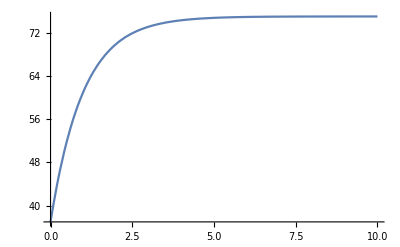

```mathematica
Plot[cc[0,t],{t,0,10},PlotRange->All]
```

```mathematica
cc[0,10]
```

74.9989

```mathematica
cc[10,10]
```

35.7533

```mathematica
a+b=75
a+b*Exp[-10]=37
```

```mathematica
N[38/(1-Exp[-10])]
```

38.0017

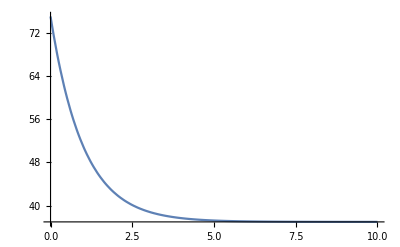

```mathematica
Plot[37+38*Exp[-t],{t,0,10},PlotRange->All]
```

```mathematica
test[t]=37+38*Exp[-t]
```

37+38 ⅇ^-t

```mathematica
test[x]
```

test[x]

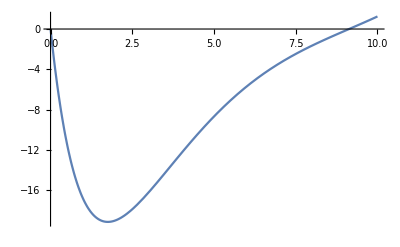

```mathematica
Plot[37+38*Exp[-x]-cc[x,10],{x,0,10}]
```

```mathematica
N[37+38*Exp[-2]]
```

42.1427

```mathematica
cc[2,10]
```

61.1434

```mathematica
ggg
```

{{1.,37.},{2.,37.},{3.,37.},{4.,37.},{5.,37.},{6.,37.},{7.,37.},{8.,37.},{9.,37.},{10.,37.},{11.,37.},{12.,37.},{13.,37.},{14.,37.},{15.,37.0033},{16.,37.0067},{17.,37.01},{18.,37.01},{19.,37.0133},{20.,37.0167},{21.,37.0233},{22.,37.0267},{23.,37.0333},{24.,37.04},{25.,37.05},{26.,37.06},{27.,37.07},{28.,37.08},{29.,37.09},{30.,37.1033},{31.,37.1167},{32.,37.1333},{33.,37.1467},{34.,37.1633},{35.,37.18},{36.,37.2},{37.,37.22},{38.,37.24},{39.,37.26},{40.,37.2833},{41.,37.3067},{42.,37.3333},{43.,37.3567},{44.,37.3833},{45.,37.41},{46.,37.4367},{47.,37.4633},{48.,37.49},{49.,37.52},{50.,37.55},{51.,37.58},{52.,37.6133},{53.,37.6467},{54.,37.68},{55.,37.71},{56.,37.7433},{57.,37.7767},{58.,37.8133},{59.,37.8467},{60.,37.88},{61.,37.9133},{62.,37.95},{63.,37.9867},{64.,38.0233},{65.,38.0567},{66.,38.0933},{67.,38.13},{68.,38.1667},{69.,38.2033},{70.,38.24},{71.,38.28},{72.,38.3167},{73.,38.3533},{74.,38.39},{75.,38.43},{76.,38.4667},{77.,38.5033},{78.,38.54},{79.,38.58},{80.,38.6167},{81.,38.6533},{82.,38.69},{83.,38.73},{84.,38.77},{85.,38.8067},{86.,38.8433},{87.,38.88},{88.,38.92},{89.,38.9567},{90.,38.9933},{91.,39.03},{92.,39.07},{93.,39.1067},{94.,39.1433},{95.,39.18},{96.,39.22},{97.,39.2567},{98.,39.2933},{99.,39.33},{100.,39.3667},{101.,39.4033},{102.,39.44},{103.,39.48},{104.,39.5167},{105.,39.5533},{106.,39.5867},{107.,39.6233},{108.,39.66},{109.,39.6967},{110.,39.7333},{111.,39.7667},{112.,39.8033},{113.,39.8367},{114.,39.8733},{115.,39.91},{116.,39.9467},{117.,39.9833},{118.,40.0167},{119.,40.0533},{120.,40.0867},{121.,40.12},{122.,40.1533},{123.,40.1867},{124.,40.2233},{125.,40.2567},{126.,40.29},{127.,40.3233},{128.,40.3567},{129.,40.3933},{130.,40.4267},{131.,40.46},{132.,40.49},{133.,40.5233},{134.,40.5567},{135.,40.59},{136.,40.6233},{137.,40.6567},{138.,40.69},{139.,40.72},{140.,40.75},{141.,40.7833},{142.,40.8167},{143.,40.85},{144.,40.88},{145.,40.91},{146.,40.94},{147.,40.97},{148.,41.},{149.,41.0333},{150.,41.0667},{151.,41.1},{152.,41.13},{153.,41.16},{154.,41.19},{155.,41.22},{156.,41.25},{157.,41.28},{158.,41.31},{159.,41.34},{160.,41.37},{161.,41.3967},{162.,41.4233},{163.,41.45},{164.,41.48},{165.,41.51},{166.,41.54},{167.,41.57},{168.,41.6},{169.,41.6267},{170.,41.6533},{171.,41.68},{172.,41.71},{173.,41.74},{174.,41.7667},{175.,41.7933},{176.,41.82},{177.,41.85},{178.,41.8767},{179.,41.9033},{180.,41.93},{181.,41.9567},{182.,41.9833},{183.,42.01},{184.,42.0367},{185.,42.0633},{186.,42.09},{187.,42.1167},{188.,42.1433},{189.,42.1667},{190.,42.1933},{191.,42.22},{192.,42.2467},{193.,42.2733},{194.,42.2967},{195.,42.3233},{196.,42.3467},{197.,42.3733},{198.,42.3967},{199.,42.4233},{200.,42.4467},{201.,42.4733},{202.,42.4967},{203.,42.52},{204.,42.5433},{205.,42.5667},{206.,42.5933},{207.,42.6167},{208.,42.6433},{209.,42.6667},{210.,42.69},{211.,42.7133},{212.,42.7367},{213.,42.76},{214.,42.7833},{215.,42.8067},{216.,42.83},{217.,42.85},{218.,42.8733},{219.,42.8967},{220.,42.92},{221.,42.9433},{222.,42.9667},{223.,42.99},{224.,43.01},{225.,43.03},{226.,43.0533},{227.,43.0767},{228.,43.1},{229.,43.12},{230.,43.14},{231.,43.1633},{232.,43.1867},{233.,43.21},{234.,43.23},{235.,43.25},{236.,43.27},{237.,43.29},{238.,43.31},{239.,43.33},{240.,43.35},{241.,43.3733},{242.,43.3967},{243.,43.42},{244.,43.44},{245.,43.46},{246.,43.48},{247.,43.5},{248.,43.52},{249.,43.54},{250.,43.56},{251.,43.58},{252.,43.6},{253.,43.62},{254.,43.64},{255.,43.6567},{256.,43.6733},{257.,43.69},{258.,43.71},{259.,43.73},{260.,43.75},{261.,43.77},{262.,43.79},{263.,43.81},{264.,43.83},{265.,43.8467},{266.,43.8633},{267.,43.88},{268.,43.9},{269.,43.92},{270.,43.94},{271.,43.9567},{272.,43.9733},{273.,43.99},{274.,44.01},{275.,44.03},{276.,44.0467},{277.,44.0633},{278.,44.08},{279.,44.1},{280.,44.1167},{281.,44.1333},{282.,44.15},{283.,44.1667},{284.,44.1833},{285.,44.2},{286.,44.22},{287.,44.2367},{288.,44.2533},{289.,44.27},{290.,44.2867},{291.,44.3033},{292.,44.32},{293.,44.3367},{294.,44.3533},{295.,44.3667},{296.,44.3833},{297.,44.4},{298.,44.4167},{299.,44.4333},{300.,44.4467},{301.,44.4633},{302.,44.48},{303.,44.4967},{304.,44.5133},{305.,44.5267},{306.,44.5433},{307.,44.5567},{308.,44.5733},{309.,44.59},{310.,44.6067},{311.,44.6233},{312.,44.6367},{313.,44.6533},{314.,44.6667},{315.,44.6833},{316.,44.6967},{317.,44.7133},{318.,44.7267},{319.,44.74},{320.,44.7533},{321.,44.7667},{322.,44.7833},{323.,44.7967},{324.,44.8133},{325.,44.8267},{326.,44.8433},{327.,44.8567},{328.,44.87},{329.,44.8833},{330.,44.8967},{331.,44.9133},{332.,44.9267},{333.,44.94},{334.,44.9533},{335.,44.9667},{336.,44.98},{337.,44.9933},{338.,45.0067},{339.,45.02},{340.,45.0333},{341.,45.0467},{342.,45.06},{343.,45.0733},{344.,45.0867},{345.,45.1},{346.,45.1133},{347.,45.1267},{348.,45.14},{349.,45.1533},{350.,45.1667},{351.,45.18},{352.,45.19},{353.,45.2033},{354.,45.2167},{355.,45.23},{356.,45.24},{357.,45.2533},{358.,45.2667},{359.,45.28},{360.,45.29},{361.,45.3},{362.,45.3133},{363.,45.3267},{364.,45.34},{365.,45.35},{366.,45.3633},{367.,45.3767},{368.,45.39},{369.,45.4},{370.,45.41},{371.,45.42},{372.,45.4333},{373.,45.4467},{374.,45.46},{375.,45.47},{376.,45.48},{377.,45.49},{378.,45.5},{379.,45.5133},{380.,45.5267},{381.,45.54},{382.,45.55},{383.,45.56},{384.,45.57},{385.,45.58},{386.,45.59},{387.,45.6},{388.,45.61},{389.,45.6233},{390.,45.6367},{391.,45.65},{392.,45.66},{393.,45.67},{394.,45.68},{395.,45.69},{396.,45.7},{397.,45.71},{398.,45.72},{399.,45.73},{400.,45.74},{401.,45.75},{402.,45.76},{403.,45.77},{404.,45.78},{405.,45.79},{406.,45.8},{407.,45.81},{408.,45.82},{409.,45.83},{410.,45.84},{411.,45.85},{412.,45.86},{413.,45.87},{414.,45.88},{415.,45.89},{416.,45.9},{417.,45.91},{418.,45.92},{419.,45.93},{420.,45.94},{421.,45.95},{422.,45.96},{423.,45.9667},{424.,45.9733},{425.,45.98},{426.,45.99},{427.,46.},{428.,46.01},{429.,46.02},{430.,46.03},{431.,46.04},{432.,46.05},{433.,46.06},{434.,46.0667},{435.,46.0733},{436.,46.08},{437.,46.09},{438.,46.1},{439.,46.11},{440.,46.12},{441.,46.1267},{442.,46.1333},{443.,46.14},{444.,46.15},{445.,46.16},{446.,46.17},{447.,46.18},{448.,46.1867},{449.,46.1933},{450.,46.2},{451.,46.21},{452.,46.22},{453.,46.2267},{454.,46.2333},{455.,46.24},{456.,46.25},{457.,46.26},{458.,46.2667},{459.,46.2733},{460.,46.28},{461.,46.29},{462.,46.3},{463.,46.3067},{464.,46.3133},{465.,46.32},{466.,46.33},{467.,46.34},{468.,46.3467},{469.,46.3533},{470.,46.36},{471.,46.37},{472.,46.3767},{473.,46.3833},{474.,46.39},{475.,46.4},{476.,46.4067},{477.,46.4133},{478.,46.42},{479.,46.4267},{480.,46.4333},{481.,46.44},{482.,46.45},{483.,46.4567},{484.,46.4633},{485.,46.47},{486.,46.4767},{487.,46.4833},{488.,46.49},{489.,46.5},{490.,46.5067},{491.,46.5133},{492.,46.52},{493.,46.5267},{494.,46.5333},{495.,46.54},{496.,46.5467},{497.,46.5533},{498.,46.56},{499.,46.5667},{500.,46.5733},{501.,46.58},{502.,46.5867},{503.,46.5933},{504.,46.6},{505.,46.6067},{506.,46.6133},{507.,46.62},{508.,46.6267},{509.,46.6333},{510.,46.6367},{511.,46.6433},{512.,46.65},{513.,46.6567},{514.,46.6633},{515.,46.67},{516.,46.6767},{517.,46.6833},{518.,46.6867},{519.,46.6933},{520.,46.7},{521.,46.7067},{522.,46.7133},{523.,46.7167},{524.,46.7233},{525.,46.73},{526.,46.7367},{527.,46.7433},{528.,46.7467},{529.,46.7533},{530.,46.76},{531.,46.7667},{532.,46.7733},{533.,46.7767},{534.,46.7833},{535.,46.7867},{536.,46.7933},{537.,46.8},{538.,46.8067},{539.,46.8133},{540.,46.8167},{541.,46.8233},{542.,46.8267},{543.,46.8333},{544.,46.8367},{545.,46.8433},{546.,46.8467},{547.,46.8533},{548.,46.86},{549.,46.8667},{550.,46.8733},{551.,46.8767},{552.,46.8833},{553.,46.8867},{554.,46.8933},{555.,46.8967},{556.,46.9033},{557.,46.9067},{558.,46.9133},{559.,46.9167},{560.,46.9233},{561.,46.9267},{562.,46.9333},{563.,46.9367},{564.,46.9433},{565.,46.9467},{566.,46.9533},{567.,46.9567},{568.,46.9633},{569.,46.9667},{570.,46.9733},{571.,46.9767},{572.,46.9833},{573.,46.9867},{574.,46.9933},{575.,46.9967},{576.,47.0033},{577.,47.0067},{578.,47.0133},{579.,47.0167},{580.,47.0233},{581.,47.0267},{582.,47.03},{583.,47.0333},{584.,47.0367},{585.,47.0433},{586.,47.0467},{587.,47.0533},{588.,47.0567},{589.,47.0633},{590.,47.0667},{591.,47.0733},{592.,47.0767},{593.,47.08},{594.,47.0833},{595.,47.0867},{596.,47.0933},{597.,47.0967},{598.,47.1033},{599.,47.1067},{600.,47.11},{601.,47.1133},{602.,47.1167},{603.,47.1233},{604.,47.1267},{605.,47.1333},{606.,47.1367},{607.,47.14},{608.,47.1433},{609.,47.1467},{610.,47.1533},{611.,47.1567},{612.,47.16},{613.,47.1633},{614.,47.1667},{615.,47.1733},{616.,47.1767},{617.,47.18},{618.,47.1833},{619.,47.1867},{620.,47.1933},{621.,47.1967},{622.,47.2},{623.,47.2033},{624.,47.2067},{625.,47.2133},{626.,47.2167},{627.,47.22},{628.,47.2233},{629.,47.2267},{630.,47.23},{631.,47.2333},{632.,47.2367},{633.,47.2433},{634.,47.2467},{635.,47.25},{636.,47.2533},{637.,47.2567},{638.,47.26},{639.,47.2633},{640.,47.2667},{641.,47.27},{642.,47.2733},{643.,47.2767},{644.,47.28},{645.,47.2833},{646.,47.2867},{647.,47.2933},{648.,47.2967},{649.,47.3},{650.,47.3033},{651.,47.3067},{652.,47.31},{653.,47.3133},{654.,47.3167},{655.,47.32},{656.,47.3233},{657.,47.3267},{658.,47.33},{659.,47.3333},{660.,47.3367},{661.,47.34},{662.,47.3433},{663.,47.3467},{664.,47.35},{665.,47.3533},{666.,47.3567},{667.,47.36},{668.,47.36},{669.,47.3633},{670.,47.3667},{671.,47.37},{672.,47.3733},{673.,47.3767},{674.,47.38},{675.,47.3833},{676.,47.3867},{677.,47.39},{678.,47.3933},{679.,47.3967},{680.,47.4},{681.,47.4},{682.,47.4033},{683.,47.4067},{684.,47.41},{685.,47.4133},{686.,47.4167},{687.,47.42},{688.,47.4233},{689.,47.4267},{690.,47.43},{691.,47.43},{692.,47.4333},{693.,47.4367},{694.,47.44},{695.,47.4433},{696.,47.4467},{697.,47.45},{698.,47.45},{699.,47.4533},{700.,47.4567},{701.,47.46},{702.,47.46},{703.,47.4633},{704.,47.4667},{705.,47.47},{706.,47.4733},{707.,47.4767},{708.,47.48},{709.,47.48},{710.,47.4833},{711.,47.4867},{712.,47.49},{713.,47.49},{714.,47.4933},{715.,47.4967},{716.,47.5},{717.,47.5},{718.,47.5033},{719.,47.5067},{720.,47.51},{721.,47.51},{722.,47.5133},{723.,47.5167},{724.,47.52},{725.,47.52},{726.,47.5233},{727.,47.5267},{728.,47.53},{729.,47.53},{730.,47.5333},{731.,47.5367},{732.,47.54},{733.,47.54},{734.,47.5433},{735.,47.5467},{736.,47.55},{737.,47.55},{738.,47.5533},{739.,47.5567},{740.,47.56},{741.,47.56},{742.,47.56},{743.,47.5633},{744.,47.5667},{745.,47.57},{746.,47.57},{747.,47.5733},{748.,47.5767},{749.,47.58},{750.,47.58},{751.,47.58},{752.,47.5833},{753.,47.5867},{754.,47.59},{755.,47.59},{756.,47.5933},{757.,47.5967},{758.,47.6},{759.,47.6},{760.,47.6},{761.,47.6033},{762.,47.6067},{763.,47.61},{764.,47.61},{765.,47.61},{766.,47.6133},{767.,47.6167},{768.,47.62},{769.,47.62},{770.,47.62},{771.,47.6233},{772.,47.6267},{773.,47.63},{774.,47.63},{775.,47.63},{776.,47.6333},{777.,47.6367},{778.,47.64},{779.,47.64},{780.,47.64},{781.,47.6433},{782.,47.6467},{783.,47.65},{784.,47.65},{785.,47.65},{786.,47.6533},{787.,47.6567},{788.,47.66},{789.,47.66},{790.,47.66},{791.,47.6633},{792.,47.6667},{793.,47.67},{794.,47.67},{795.,47.67},{796.,47.67},{797.,47.6733},{798.,47.6767},{799.,47.68},{800.,47.68},{801.,47.68},{802.,47.68},{803.,47.6833},{804.,47.6867},{805.,47.69},{806.,47.69},{807.,47.69},{808.,47.6933},{809.,47.6967},{810.,47.7},{811.,47.7},{812.,47.7},{813.,47.7},{814.,47.7033},{815.,47.7067},{816.,47.71},{817.,47.71},{818.,47.71},{819.,47.71},{820.,47.7133},{821.,47.7167},{822.,47.72},{823.,47.72},{824.,47.72},{825.,47.72},{826.,47.72},{827.,47.7233},{828.,47.7267},{829.,47.73},{830.,47.73},{831.,47.73},{832.,47.73},{833.,47.7333},{834.,47.7367},{835.,47.74},{836.,47.74},{837.,47.74},{838.,47.74},{839.,47.74},{840.,47.7433},{841.,47.7467},{842.,47.75},{843.,47.75},{844.,47.75},{845.,47.75},{846.,47.7533},{847.,47.7567},{848.,47.76},{849.,47.76},{850.,47.76},{851.,47.76},{852.,47.76},{853.,47.7633},{854.,47.7667},{855.,47.77},{856.,47.77},{857.,47.77},{858.,47.77},{859.,47.77},{860.,47.77},{861.,47.7733},{862.,47.7767},{863.,47.78},{864.,47.78},{865.,47.78},{866.,47.78},{867.,47.78},{868.,47.7833},{869.,47.7867},{870.,47.79},{871.,47.79},{872.,47.79},{873.,47.79},{874.,47.79},{875.,47.79},{876.,47.7933},{877.,47.7967},{878.,47.8},{879.,47.8},{880.,47.8},{881.,47.8},{882.,47.8},{883.,47.8},{884.,47.8033},{885.,47.8067},{886.,47.81},{887.,47.81},{888.,47.81},{889.,47.81},{890.,47.81},{891.,47.81},{892.,47.8133},{893.,47.8167},{894.,47.82},{895.,47.82},{896.,47.82},{897.,47.82},{898.,47.82},{899.,47.82},{900.,47.82},{901.,47.8233},{902.,47.8267},{903.,47.83},{904.,47.83},{905.,47.83},{906.,47.83},{907.,47.83},{908.,47.83},{909.,47.83},{910.,47.8333},{911.,47.8367},{912.,47.84},{913.,47.84},{914.,47.84},{915.,47.84},{916.,47.84},{917.,47.84},{918.,47.84},{919.,47.8433},{920.,47.8467},{921.,47.85},{922.,47.85},{923.,47.85},{924.,47.85},{925.,47.85},{926.,47.85},{927.,47.85},{928.,47.85},{929.,47.8533},{930.,47.8567},{931.,47.86},{932.,47.86},{933.,47.86},{934.,47.86},{935.,47.86},{936.,47.86},{937.,47.86},{938.,47.86},{939.,47.8633},{940.,47.8667},{941.,47.87},{942.,47.87},{943.,47.87},{944.,47.87},{945.,47.87},{946.,47.87},{947.,47.87},{948.,47.87},{949.,47.87},{950.,47.8733},{951.,47.8767},{952.,47.88},{953.,47.88},{954.,47.88},{955.,47.88},{956.,47.88},{957.,47.88},{958.,47.88},{959.,47.88},{960.,47.88},{961.,47.8833},{962.,47.8867},{963.,47.89},{964.,47.89},{965.,47.89},{966.,47.89},{967.,47.89},{968.,47.89},{969.,47.89},{970.,47.89},{971.,47.89},{972.,47.8933},{973.,47.8967},{974.,47.9},{975.,47.9},{976.,47.9},{977.,47.9},{978.,47.9},{979.,47.9},{980.,47.9},{981.,47.9},{982.,47.9},{983.,47.9},{984.,47.9},{985.,47.9033},{986.,47.9067},{987.,47.91},{988.,47.91},{989.,47.91},{990.,47.91},{991.,47.91},{992.,47.91},{993.,47.91},{994.,47.91},{995.,47.91},{996.,47.91},{997.,47.91},{998.,47.9133},{999.,47.9167},{1000.,47.92},{1001.,47.92},{1002.,47.92},{1003.,47.92},{1004.,47.92},{1005.,47.92},{1006.,47.92},{1007.,47.92},{1008.,47.92},{1009.,47.92},{1010.,47.92},{1011.,47.9233},{1012.,47.9267},{1013.,47.93},{1014.,47.93},{1015.,47.93},{1016.,47.93},{1017.,47.93},{1018.,47.93},{1019.,47.93},{1020.,47.93},{1021.,47.93},{1022.,47.93},{1023.,47.93},{1024.,47.93},{1025.,47.93},{1026.,47.9333},{1027.,47.9367},{1028.,47.94},{1029.,47.94},{1030.,47.94},{1031.,47.94},{1032.,47.94},{1033.,47.94},{1034.,47.94},{1035.,47.94},{1036.,47.94},{1037.,47.94},{1038.,47.94},{1039.,47.94},{1040.,47.94},{1041.,47.94},{1042.,47.9433},{1043.,47.9467},{1044.,47.95},{1045.,47.95},{1046.,47.95},{1047.,47.95},{1048.,47.95},{1049.,47.95},{1050.,47.95},{1051.,47.95},{1052.,47.95},{1053.,47.95},{1054.,47.95},{1055.,47.95},{1056.,47.95},{1057.,47.95},{1058.,47.95},{1059.,47.9533},{1060.,47.9567},{1061.,47.96},{1062.,47.96},{1063.,47.96},{1064.,47.96},{1065.,47.96},{1066.,47.96},{1067.,47.96},{1068.,47.96},{1069.,47.96},{1070.,47.96},{1071.,47.96},{1072.,47.96},{1073.,47.96},{1074.,47.96},{1075.,47.96},{1076.,47.96},{1077.,47.9633},{1078.,47.9667},{1079.,47.97},{1080.,47.97},{1081.,47.97},{1082.,47.97},{1083.,47.97},{1084.,47.97},{1085.,47.97},{1086.,47.97},{1087.,47.97},{1088.,47.97},{1089.,47.97},{1090.,47.97},{1091.,47.97},{1092.,47.97},{1093.,47.97},{1094.,47.97},{1095.,47.97},{1096.,47.97},{1097.,47.9733},{1098.,47.9767},{1099.,47.98},{1100.,47.98},{1101.,47.98},{1102.,47.98},{1103.,47.98},{1104.,47.98},{1105.,47.98},{1106.,47.98},{1107.,47.98},{1108.,47.98},{1109.,47.98},{1110.,47.98},{1111.,47.98},{1112.,47.98},{1113.,47.98},{1114.,47.98},{1115.,47.98},{1116.,47.98},{1117.,47.98},{1118.,47.98},{1119.,47.9833},{1120.,47.9867},{1121.,47.99},{1122.,47.99},{1123.,47.99},{1124.,47.99},{1125.,47.99},{1126.,47.99},{1127.,47.99},{1128.,47.99},{1129.,47.99},{1130.,47.99},{1131.,47.99},{1132.,47.99},{1133.,47.99},{1134.,47.99},{1135.,47.99},{1136.,47.99},{1137.,47.99},{1138.,47.99},{1139.,47.99},{1140.,47.99},{1141.,47.99},{1142.,47.99},{1143.,47.9933},{1144.,47.9967},{1145.,48.},{1146.,48.},{1147.,48.},{1148.,48.},{1149.,48.},{1150.,48.},{1151.,48.},{1152.,48.},{1153.,48.},{1154.,48.},{1155.,48.},{1156.,48.},{1157.,48.},{1158.,48.},{1159.,48.},{1160.,48.},{1161.,48.},{1162.,48.},{1163.,48.},{1164.,48.},{1165.,48.},{1166.,48.},{1167.,48.},{1168.,48.},{1169.,48.},{1170.,48.0033},{1171.,48.0067},{1172.,48.01},{1173.,48.01},{1174.,48.01},{1175.,48.01},{1176.,48.01},{1177.,48.01},{1178.,48.01},{1179.,48.01},{1180.,48.01},{1181.,48.01},{1182.,48.01},{1183.,48.01},{1184.,48.01},{1185.,48.01},{1186.,48.01},{1187.,48.01},{1188.,48.01},{1189.,48.01},{1190.,48.01},{1191.,48.01},{1192.,48.01},{1193.,48.01},{1194.,48.01},{1195.,48.01},{1196.,48.01},{1197.,48.01},{1198.,48.01},{1199.,48.01},{1200.,48.0133},{1201.,48.0167},{1202.,48.02},{1203.,48.02},{1204.,48.02},{1205.,48.02},{1206.,48.02},{1207.,48.02},{1208.,48.02},{1209.,48.02},{1210.,48.02},{1211.,48.02},{1212.,48.02},{1213.,48.02},{1214.,48.02},{1215.,48.02},{1216.,48.02},{1217.,48.02},{1218.,48.02},{1219.,48.02},{1220.,48.02},{1221.,48.02},{1222.,48.02},{1223.,48.02},{1224.,48.02},{1225.,48.02},{1226.,48.02},{1227.,48.02},{1228.,48.02},{1229.,48.02},{1230.,48.02},{1231.,48.02},{1232.,48.02},{1233.,48.02},{1234.,48.02},{1235.,48.0233},{1236.,48.0267},{1237.,48.03},{1238.,48.03},{1239.,48.03},{1240.,48.03},{1241.,48.03},{1242.,48.03},{1243.,48.03},{1244.,48.03},{1245.,48.03},{1246.,48.03},{1247.,48.03},{1248.,48.03},{1249.,48.03},{1250.,48.03},{1251.,48.03},{1252.,48.03},{1253.,48.03},{1254.,48.03},{1255.,48.03},{1256.,48.03},{1257.,48.03},{1258.,48.03},{1259.,48.03},{1260.,48.03},{1261.,48.03},{1262.,48.03},{1263.,48.03},{1264.,48.03},{1265.,48.03},{1266.,48.03},{1267.,48.03},{1268.,48.03},{1269.,48.03},{1270.,48.03},{1271.,48.03},{1272.,48.03},{1273.,48.03},{1274.,48.03},{1275.,48.03},{1276.,48.03},{1277.,48.0333},{1278.,48.0367},{1279.,48.04},{1280.,48.04},{1281.,48.04},{1282.,48.04},{1283.,48.04},{1284.,48.04},{1285.,48.04},{1286.,48.04},{1287.,48.04},{1288.,48.04},{1289.,48.04},{1290.,48.04},{1291.,48.04},{1292.,48.04},{1293.,48.04},{1294.,48.04},{1295.,48.04},{1296.,48.04},{1297.,48.04},{1298.,48.04},{1299.,48.04},{1300.,48.04},{1301.,48.04},{1302.,48.04},{1303.,48.04},{1304.,48.04},{1305.,48.04},{1306.,48.04},{1307.,48.04},{1308.,48.04},{1309.,48.04},{1310.,48.04},{1311.,48.04},{1312.,48.04},{1313.,48.04},{1314.,48.04},{1315.,48.04},{1316.,48.04},{1317.,48.04},{1318.,48.04},{1319.,48.04},{1320.,48.04},{1321.,48.04},{1322.,48.04},{1323.,48.04},{1324.,48.04},{1325.,48.04},{1326.,48.04},{1327.,48.04},{1328.,48.0433},{1329.,48.0467},{1330.,48.05},{1331.,48.05},{1332.,48.05},{1333.,48.05},{1334.,48.05},{1335.,48.05},{1336.,48.05},{1337.,48.05},{1338.,48.05},{1339.,48.05},{1340.,48.05},{1341.,48.05},{1342.,48.05},{1343.,48.05},{1344.,48.05},{1345.,48.05},{1346.,48.05},{1347.,48.05},{1348.,48.05},{1349.,48.05},{1350.,48.05},{1351.,48.05},{1352.,48.05},{1353.,48.05},{1354.,48.05},{1355.,48.05},{1356.,48.05},{1357.,48.05},{1358.,48.05},{1359.,48.05},{1360.,48.05},{1361.,48.05},{1362.,48.05},{1363.,48.05},{1364.,48.05},{1365.,48.05},{1366.,48.05},{1367.,48.05},{1368.,48.05},{1369.,48.05},{1370.,48.05},{1371.,48.05},{1372.,48.05},{1373.,48.05},{1374.,48.05},{1375.,48.05},{1376.,48.05},{1377.,48.05},{1378.,48.05},{1379.,48.05},{1380.,48.05},{1381.,48.05},{1382.,48.05},{1383.,48.05},{1384.,48.05},{1385.,48.05},{1386.,48.05},{1387.,48.05},{1388.,48.05},{1389.,48.05},{1390.,48.05},{1391.,48.05},{1392.,48.05},{1393.,48.0533},{1394.,48.0567},{1395.,48.06},{1396.,48.06},{1397.,48.06},{1398.,48.06},{1399.,48.06},{1400.,48.06},{1401.,48.06},{1402.,48.06},{1403.,48.06},{1404.,48.06},{1405.,48.06},{1406.,48.06},{1407.,48.06},{1408.,48.06},{1409.,48.06},{1410.,48.06},{1411.,48.06},{1412.,48.06},{1413.,48.06},{1414.,48.06},{1415.,48.06},{1416.,48.06},{1417.,48.06},{1418.,48.06},{1419.,48.06},{1420.,48.06},{1421.,48.06},{1422.,48.06},{1423.,48.06},{1424.,48.06},{1425.,48.06},{1426.,48.06},{1427.,48.06},{1428.,48.06},{1429.,48.06},{1430.,48.06},{1431.,48.06},{1432.,48.06},{1433.,48.06},{1434.,48.06},{1435.,48.06},{1436.,48.06},{1437.,48.06},{1438.,48.06},{1439.,48.06},{1440.,48.06},{1441.,48.06},{1442.,48.06},{1443.,48.06},{1444.,48.06},{1445.,48.06},{1446.,48.06},{1447.,48.06},{1448.,48.06},{1449.,48.06},{1450.,48.06},{1451.,48.06},{1452.,48.06},{1453.,48.06},{1454.,48.06},{1455.,48.06},{1456.,48.06},{1457.,48.06},{1458.,48.06},{1459.,48.06},{1460.,48.06},{1461.,48.06},{1462.,48.06},{1463.,48.06},{1464.,48.06},{1465.,48.06},{1466.,48.06},{1467.,48.06},{1468.,48.06},{1469.,48.06},{1470.,48.06},{1471.,48.06},{1472.,48.06},{1473.,48.06},{1474.,48.06},{1475.,48.06},{1476.,48.06},{1477.,48.06},{1478.,48.06},{1479.,48.06},{1480.,48.06},{1481.,48.06},{1482.,48.06},{1483.,48.06},{1484.,48.06},{1485.,48.06},{1486.,48.0633},{1487.,48.0667},{1488.,48.07},{1489.,48.07},{1490.,48.07},{1491.,48.07},{1492.,48.07},{1493.,48.07},{1494.,48.07},{1495.,48.07},{1496.,48.07},{1497.,48.07},{1498.,48.07},{1499.,48.07},{1500.,48.07},{1501.,48.07},{1502.,48.07},{1503.,48.07},{1504.,48.07},{1505.,48.07},{1506.,48.07},{1507.,48.07},{1508.,48.07},{1509.,48.07},{1510.,48.07},{1511.,48.07},{1512.,48.07},{1513.,48.07},{1514.,48.07},{1515.,48.07},{1516.,48.07},{1517.,48.07},{1518.,48.07},{1519.,48.07},{1520.,48.07},{1521.,48.07},{1522.,48.07},{1523.,48.07},{1524.,48.07},{1525.,48.07},{1526.,48.07},{1527.,48.07},{1528.,48.07},{1529.,48.07},{1530.,48.07},{1531.,48.07},{1532.,48.07},{1533.,48.07},{1534.,48.07},{1535.,48.07},{1536.,48.07},{1537.,48.07},{1538.,48.07},{1539.,48.07},{1540.,48.07},{1541.,48.07},{1542.,48.07},{1543.,48.07},{1544.,48.07},{1545.,48.07},{1546.,48.07},{1547.,48.07},{1548.,48.07},{1549.,48.07},{1550.,48.07},{1551.,48.07},{1552.,48.07},{1553.,48.07},{1554.,48.07},{1555.,48.07},{1556.,48.07},{1557.,48.07},{1558.,48.07},{1559.,48.07},{1560.,48.07},{1561.,48.07},{1562.,48.07},{1563.,48.07},{1564.,48.07},{1565.,48.07},{1566.,48.07},{1567.,48.07},{1568.,48.07},{1569.,48.07},{1570.,48.07},{1571.,48.07},{1572.,48.07},{1573.,48.07},{1574.,48.07},{1575.,48.07},{1576.,48.07},{1577.,48.07},{1578.,48.07},{1579.,48.07},{1580.,48.07},{1581.,48.07},{1582.,48.07},{1583.,48.07},{1584.,48.07},{1585.,48.07},{1586.,48.07},{1587.,48.07},{1588.,48.07},{1589.,48.07},{1590.,48.07},{1591.,48.07},{1592.,48.07},{1593.,48.07},{1594.,48.07},{1595.,48.07},{1596.,48.07},{1597.,48.07},{1598.,48.07},{1599.,48.07},{1600.,48.07},{1601.,48.07},{1602.,48.07},{1603.,48.07},{1604.,48.07},{1605.,48.07},{1606.,48.07},{1607.,48.07},{1608.,48.07},{1609.,48.07},{1610.,48.07},{1611.,48.07},{1612.,48.07},{1613.,48.07},{1614.,48.07},{1615.,48.07},{1616.,48.07},{1617.,48.07},{1618.,48.07},{1619.,48.07},{1620.,48.07},{1621.,48.07},{1622.,48.07},{1623.,48.07},{1624.,48.07},{1625.,48.07},{1626.,48.07},{1627.,48.07},{1628.,48.07},{1629.,48.07},{1630.,48.07},{1631.,48.07},{1632.,48.07},{1633.,48.07},{1634.,48.07},{1635.,48.07},{1636.,48.07},{1637.,48.07},{1638.,48.07},{1639.,48.07},{1640.,48.07},{1641.,48.07},{1642.,48.07},{1643.,48.07}}

```mathematica
diff[i_]:=Module[
{j,k,cur,result},
{
j=i;
k=i;
result=0;
cur=data[[1]][[j]][[2]];
While[
cur==data[[1]][[j]][[2]],
{
If[j>1647,break];
j=j+1;
}
];
result=data[[1]][[j]][[2]]-cur;
};
result/(j-k)
]
```

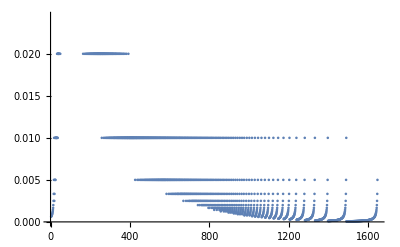

```mathematica
g1=Table[{i,diff[i]},{i,3,1646}];
ListPlot[g1]
```

```mathematica
g1
```

{{3,0.000625},{4,0.000666667},{5,0.000714286},{6,0.000769231},{7,0.000833333},{8,0.000909091},{9,0.001},{10,0.00111111},{11,0.00125},{12,0.00142857},{13,0.00166667},{14,0.002},{15,0.0025},{16,0.00333333},{17,0.005},{18,0.01},{19,0.0025},{20,0.00333333},{21,0.005},{22,0.01},{23,0.005},{24,0.01},{25,0.005},{26,0.01},{27,0.01},{28,0.01},{29,0.01},{30,0.01},{31,0.01},{32,0.01},{33,0.02},{34,0.01},{35,0.02},{36,0.01},{37,0.02},{38,0.02},{39,0.02},{40,0.02},{41,0.02},{42,0.02},{43,0.03},{44,0.02},{45,0.03},{46,0.02},{47,0.03},{48,0.03},{49,0.02},{50,0.03},{51,0.03},{52,0.03},{53,0.03},{54,0.03},{55,0.04},{56,0.03},{57,0.03},{58,0.03},{59,0.04},{60,0.03},{61,0.04},{62,0.03},{63,0.03},{64,0.04},{65,0.04},{66,0.03},{67,0.04},{68,0.03},{69,0.04},{70,0.04},{71,0.03},{72,0.04},{73,0.04},{74,0.04},{75,0.03},{76,0.04},{77,0.04},{78,0.04},{79,0.03},{80,0.04},{81,0.04},{82,0.04},{83,0.03},{84,0.04},{85,0.04},{86,0.04},{87,0.04},{88,0.03},{89,0.04},{90,0.04},{91,0.04},{92,0.03},{93,0.04},{94,0.04},{95,0.04},{96,0.03},{97,0.04},{98,0.04},{99,0.04},{100,0.03},{101,0.04},{102,0.04},{103,0.03},{104,0.04},{105,0.04},{106,0.04},{107,0.03},{108,0.04},{109,0.03},{110,0.04},{111,0.04},{112,0.03},{113,0.04},{114,0.03},{115,0.04},{116,0.03},{117,0.04},{118,0.04},{119,0.03},{120,0.04},{121,0.03},{122,0.04},{123,0.03},{124,0.03},{125,0.04},{126,0.03},{127,0.04},{128,0.03},{129,0.03},{130,0.04},{131,0.03},{132,0.04},{133,0.03},{134,0.03},{135,0.03},{136,0.04},{137,0.03},{138,0.03},{139,0.04},{140,0.03},{141,0.03},{142,0.03},{143,0.03},{144,0.04},{145,0.03},{146,0.03},{147,0.03},{148,0.03},{149,0.03},{150,0.03},{151,0.03},{152,0.04},{153,0.03},{154,0.03},{155,0.03},{156,0.03},{157,0.03},{158,0.03},{159,0.03},{160,0.03},{161,0.03},{162,0.03},{163,0.03},{164,0.02},{165,0.03},{166,0.03},{167,0.03},{168,0.03},{169,0.03},{170,0.03},{171,0.03},{172,0.02},{173,0.03},{174,0.03},{175,0.03},{176,0.03},{177,0.02},{178,0.03},{179,0.03},{180,0.03},{181,0.02},{182,0.03},{183,0.03},{184,0.02},{185,0.03},{186,0.03},{187,0.02},{188,0.03},{189,0.03},{190,0.02},{191,0.03},{192,0.02},{193,0.03},{194,0.03},{195,0.02},{196,0.03},{197,0.02},{198,0.03},{199,0.02},{200,0.03}}

```mathematica
nlm0=NonlinearModelFit[g1,a+b*Exp[c*x+d],{a,b,c,d},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[0.0275533-2.09684×10^-57 ⅇ^(-47.0347+0.998585 x)]

```mathematica
nlm0["EstimatedVariance"]
```

0.000101833

```mathematica
ratio=Table[{48.08-data[[1]][[i]][[2]],data[[1]][[i+1]][[2]]-data[[1]][[i]][[2]]},{i,100,500}];
```

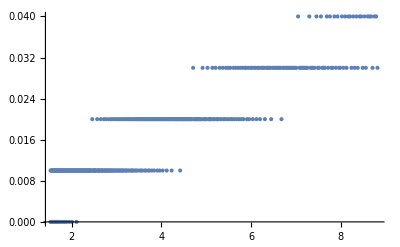

```mathematica
ListPlot[ratio]
```

```mathematica
r1=Table[{i,(data[[1]][[i+1]][[2]]-data[[1]][[i]][[2]])/(48.08-data[[1]][[i]][[2]])},{i,100,500}];
```

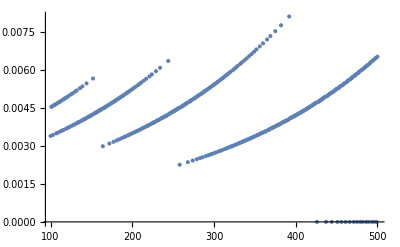

```mathematica
ListPlot[r1]
```

```mathematica
r2=Table[{i,(data[[1]][[i+1]][[2]]-data[[1]][[i]][[2]])/(48.08-data[[1]][[i]][[2]])},{i,500,750}];
```

```mathematica
rr2=Select[r2,#[[2]]>0&];
```

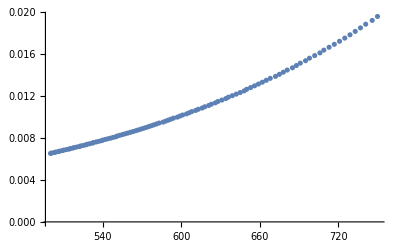

```mathematica
ListPlot[rr2]
```

```mathematica
NonlinearModelFit[r2,a+b*Exp[c*x+d],{a,b,c,d},x]
```

FittedModel[0.00442913+53022.5 ⅇ^(-53021.5+1. x)]

```mathematica
nlm2=NonlinearModelFit[rr2,a+b*Exp[c*x+d],{a,b,c,d},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[2.01019×10^246-5.49471×10^-28 ⅇ^(-71.6878+0.999947 x)]

```mathematica
FindFit[r2,a+b*Exp[c*x+d],{a,b,c,d},x]
```

{a→0.00442913,b→53022.5,c→1.,d→-53021.5}

```mathematica
r3=Table[{i,(data[[1]][[i+1]][[2]]-data[[1]][[i]][[2]])/(48.08-data[[1]][[i]][[2]])},{i,750,1000}];
```

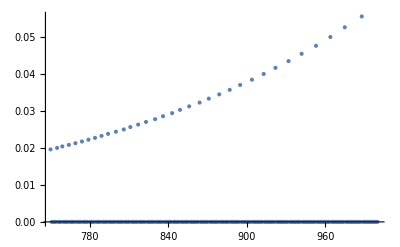

```mathematica
ListPlot[r3]
```

```mathematica
nlm3=NonlinearModelFit[r3,a+b*Exp[c*x+d],{a,b,c,d},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[-4.36587906605031×10^359-3.91582×10^-36 ⅇ^(-49.9889+1. x)]

```mathematica
r4=Table[{i,(data[[1]][[i+1]][[2]]-data[[1]][[i]][[2]])/(48.08-data[[1]][[i]][[2]])},{i,1000,1647}];
```

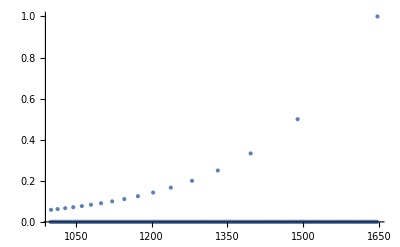

```mathematica
ListPlot[r4]
```

```mathematica
tangent[i_]:=Module[
{ii,jj,kk,r},
{
ii=i;
jj=i;
kk=i;
While[
data[[1]][[kk]][[2]]==data[[1]][[ii]][[2]],
ii++
];
While[
data[[1]][[kk]][[2]]==data[[1]][[jj]][[2]],
jj--
]
};
(data[[1]][[ii]][[2]]-data[[1]][[kk]][[2]])/(ii-jj-1)
]
```

```mathematica
gg=Table[{i,tangent[i]},{i,4,1646}];
```

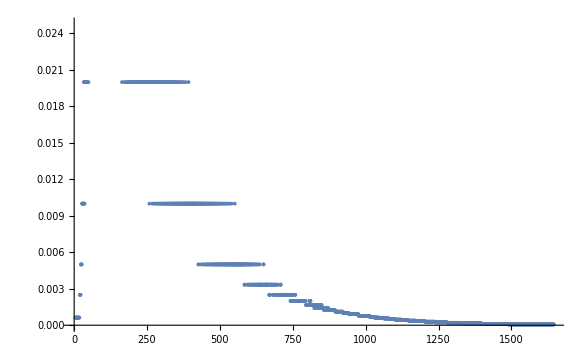

```mathematica
ListPlot[gg]
```

```mathematica
gg
```

{{4,0.000625},{5,0.000625},{6,0.000625},{7,0.000625},{8,0.000625},{9,0.000625},{10,0.000625},{11,0.000625},{12,0.000625},{13,0.000625},{14,0.000625},{15,0.000625},{16,0.000625},{17,0.000625},{18,0.000625},{19,0.0025},{20,0.0025},{21,0.0025},{22,0.0025},{23,0.005},{24,0.005},{25,0.005},{26,0.005},{27,0.01},{28,0.01},{29,0.01},{30,0.01},{31,0.01},{32,0.01},{33,0.02},{34,0.01},{35,0.02},{36,0.01},{37,0.02},{38,0.02},{39,0.02},{40,0.02},{41,0.02},{42,0.02},{43,0.03},{44,0.02},{45,0.03},{46,0.02},{47,0.03},{48,0.03},{49,0.02},{50,0.03},{51,0.03},{52,0.03},{53,0.03},{54,0.03},{55,0.04},{56,0.03},{57,0.03},{58,0.03},{59,0.04},{60,0.03},{61,0.04},{62,0.03},{63,0.03},{64,0.04},{65,0.04},{66,0.03},{67,0.04},{68,0.03},{69,0.04},{70,0.04},{71,0.03},{72,0.04},{73,0.04},{74,0.04},{75,0.03},{76,0.04},{77,0.04},{78,0.04},{79,0.03},{80,0.04},{81,0.04},{82,0.04},{83,0.03},{84,0.04},{85,0.04},{86,0.04},{87,0.04},{88,0.03},{89,0.04},{90,0.04},{91,0.04},{92,0.03},{93,0.04},{94,0.04},{95,0.04},{96,0.03},{97,0.04},{98,0.04},{99,0.04},{100,0.03},{101,0.04},{102,0.04},{103,0.03},{104,0.04},{105,0.04},{106,0.04},{107,0.03},{108,0.04},{109,0.03},{110,0.04},{111,0.04},{112,0.03},{113,0.04},{114,0.03},{115,0.04},{116,0.03},{117,0.04},{118,0.04},{119,0.03},{120,0.04},{121,0.03},{122,0.04},{123,0.03},{124,0.03},{125,0.04},{126,0.03},{127,0.04},{128,0.03},{129,0.03},{130,0.04},{131,0.03},{132,0.04},{133,0.03},{134,0.03},{135,0.03},{136,0.04},{137,0.03},{138,0.03},{139,0.04},{140,0.03},{141,0.03},{142,0.03},{143,0.03},{144,0.04},{145,0.03},{146,0.03},{147,0.03},{148,0.03},{149,0.03},{150,0.03},{151,0.03},{152,0.04},{153,0.03},{154,0.03},{155,0.03},{156,0.03},{157,0.03},{158,0.03},{159,0.03},{160,0.03},{161,0.03},{162,0.03},{163,0.03},{164,0.02},{165,0.03},{166,0.03},{167,0.03},{168,0.03},{169,0.03},{170,0.03},{171,0.03},{172,0.02},{173,0.03},{174,0.03},{175,0.03},{176,0.03},{177,0.02},{178,0.03},{179,0.03},{180,0.03},{181,0.02},{182,0.03},{183,0.03},{184,0.02},{185,0.03},{186,0.03},{187,0.02},{188,0.03},{189,0.03},{190,0.02},{191,0.03},{192,0.02},{193,0.03},{194,0.03},{195,0.02},{196,0.03},{197,0.02},{198,0.03},{199,0.02},{200,0.03},{201,0.02},{202,0.03},{203,0.02},{204,0.03},{205,0.02},{206,0.02},{207,0.03},{208,0.02},{209,0.03},{210,0.02},{211,0.03},{212,0.02},{213,0.02},{214,0.03},{215,0.02},{216,0.02},{217,0.03},{218,0.02},{219,0.02},{220,0.02},{221,0.03},{222,0.02},{223,0.02},{224,0.03},{225,0.02},{226,0.02},{227,0.02},{228,0.02},{229,0.03},{230,0.02},{231,0.02},{232,0.02},{233,0.02},{234,0.03},{235,0.02},{236,0.02},{237,0.02},{238,0.02},{239,0.02},{240,0.02},{241,0.02},{242,0.02},{243,0.02},{244,0.03},{245,0.02},{246,0.02},{247,0.02},{248,0.02},{249,0.02},{250,0.02},{251,0.02},{252,0.02},{253,0.02},{254,0.02},{255,0.02},{256,0.02},{257,0.02},{258,0.01},{259,0.02},{260,0.02},{261,0.02},{262,0.02},{263,0.02},{264,0.02},{265,0.02},{266,0.02},{267,0.02},{268,0.01},{269,0.02},{270,0.02},{271,0.02},{272,0.02},{273,0.02},{274,0.01},{275,0.02},{276,0.02},{277,0.02},{278,0.02},{279,0.01},{280,0.02},{281,0.02},{282,0.02},{283,0.01},{284,0.02},{285,0.02},{286,0.01},{287,0.02},{288,0.02},{289,0.02},{290,0.01},{291,0.02},{292,0.02},{293,0.01},{294,0.02},{295,0.02},{296,0.01},{297,0.02},{298,0.01},{299,0.02},{300,0.02},{301,0.01},{302,0.02},{303,0.01},{304,0.02},{305,0.02},{306,0.01},{307,0.02},{308,0.01},{309,0.02},{310,0.01},{311,0.02},{312,0.02},{313,0.01},{314,0.02},{315,0.01},{316,0.02},{317,0.01},{318,0.02},{319,0.01},{320,0.02},{321,0.01},{322,0.01},{323,0.02},{324,0.01},{325,0.02},{326,0.01},{327,0.02},{328,0.01},{329,0.02},{330,0.01},{331,0.01},{332,0.02},{333,0.01},{334,0.02},{335,0.01},{336,0.01},{337,0.02},{338,0.01},{339,0.01},{340,0.02},{341,0.01},{342,0.01},{343,0.02},{344,0.01},{345,0.01},{346,0.02},{347,0.01},{348,0.01},{349,0.02},{350,0.01},{351,0.01},{352,0.02},{353,0.01},{354,0.01},{355,0.01},{356,0.02},{357,0.01},{358,0.01},{359,0.01},{360,0.02},{361,0.01},{362,0.01},{363,0.01},{364,0.01},{365,0.02},{366,0.01},{367,0.01},{368,0.01},{369,0.02},{370,0.01},{371,0.01},{372,0.01},{373,0.01},{374,0.01},{375,0.02},{376,0.01},{377,0.01},{378,0.01},{379,0.01},{380,0.01},{381,0.01},{382,0.02},{383,0.01},{384,0.01},{385,0.01},{386,0.01},{387,0.01},{388,0.01},{389,0.01},{390,0.01},{391,0.01},{392,0.02},{393,0.01},{394,0.01},{395,0.01},{396,0.01},{397,0.01},{398,0.01},{399,0.01},{400,0.01},{401,0.01},{402,0.01},{403,0.01},{404,0.01},{405,0.01},{406,0.01},{407,0.01},{408,0.01},{409,0.01},{410,0.01},{411,0.01},{412,0.01},{413,0.01},{414,0.01},{415,0.01},{416,0.01},{417,0.01},{418,0.01},{419,0.01},{420,0.01},{421,0.01},{422,0.01},{423,0.01},{424,0.01},{425,0.01},{426,0.005},{427,0.005},{428,0.01},{429,0.01},{430,0.01},{431,0.01},{432,0.01},{433,0.01},{434,0.01},{435,0.01},{436,0.01},{437,0.005},{438,0.005},{439,0.01},{440,0.01},{441,0.01},{442,0.01},{443,0.01},{444,0.005},{445,0.005},{446,0.01},{447,0.01},{448,0.01},{449,0.01},{450,0.01},{451,0.005},{452,0.005},{453,0.01},{454,0.01},{455,0.01},{456,0.005},{457,0.005},{458,0.01},{459,0.01},{460,0.01},{461,0.005},{462,0.005},{463,0.01},{464,0.01},{465,0.01},{466,0.005},{467,0.005},{468,0.01},{469,0.01},{470,0.01},{471,0.005},{472,0.005},{473,0.01},{474,0.01},{475,0.005},{476,0.005},{477,0.01},{478,0.01},{479,0.005},{480,0.005},{481,0.01},{482,0.005},{483,0.005},{484,0.01},{485,0.01},{486,0.005},{487,0.005},{488,0.01},{489,0.005},{490,0.005},{491,0.01},{492,0.01},{493,0.005},{494,0.005},{495,0.01},{496,0.005},{497,0.005},{498,0.01},{499,0.005},{500,0.005},{501,0.01},{502,0.005},{503,0.005},{504,0.01},{505,0.005},{506,0.005},{507,0.01},{508,0.005},{509,0.005},{510,0.01},{511,0.005},{512,0.005},{513,0.005},{514,0.005},{515,0.01},{516,0.005},{517,0.005},{518,0.01},{519,0.005},{520,0.005},{521,0.005},{522,0.005},{523,0.01},{524,0.005},{525,0.005},{526,0.005},{527,0.005},{528,0.01},{529,0.005},{530,0.005},{531,0.005},{532,0.005},{533,0.01},{534,0.005},{535,0.005},{536,0.005},{537,0.005},{538,0.005},{539,0.005},{540,0.01},{541,0.005},{542,0.005},{543,0.005},{544,0.005},{545,0.005},{546,0.005},{547,0.005},{548,0.005},{549,0.005},{550,0.005},{551,0.01},{552,0.005},{553,0.005},{554,0.005},{555,0.005},{556,0.005},{557,0.005},{558,0.005},{559,0.005},{560,0.005},{561,0.005},{562,0.005},{563,0.005},{564,0.005},{565,0.005},{566,0.005},{567,0.005},{568,0.005},{569,0.005},{570,0.005},{571,0.005},{572,0.005},{573,0.005},{574,0.005},{575,0.005},{576,0.005},{577,0.005},{578,0.005},{579,0.005},{580,0.005},{581,0.005},{582,0.005},{583,0.005},{584,0.00333333},{585,0.00333333},{586,0.00333333},{587,0.005},{588,0.005},{589,0.005},{590,0.005},{591,0.005},{592,0.005},{593,0.005},{594,0.005},{595,0.00333333},{596,0.00333333},{597,0.00333333},{598,0.005},{599,0.005},{600,0.005},{601,0.005},{602,0.00333333},{603,0.00333333},{604,0.00333333},{605,0.005},{606,0.005},{607,0.005},{608,0.005},{609,0.00333333},{610,0.00333333},{611,0.00333333},{612,0.005},{613,0.005},{614,0.00333333},{615,0.00333333},{616,0.00333333},{617,0.005},{618,0.005},{619,0.00333333},{620,0.00333333},{621,0.00333333},{622,0.005},{623,0.005},{624,0.00333333},{625,0.00333333},{626,0.00333333},{627,0.005},{628,0.005},{629,0.00333333},{630,0.00333333},{631,0.00333333},{632,0.00333333},{633,0.00333333},{634,0.00333333},{635,0.005},{636,0.005},{637,0.00333333},{638,0.00333333},{639,0.00333333},{640,0.00333333},{641,0.00333333},{642,0.00333333},{643,0.00333333},{644,0.00333333},{645,0.00333333},{646,0.00333333},{647,0.00333333},{648,0.00333333},{649,0.005},{650,0.005},{651,0.00333333},{652,0.00333333},{653,0.00333333},{654,0.00333333},{655,0.00333333},{656,0.00333333},{657,0.00333333},{658,0.00333333},{659,0.00333333},{660,0.00333333},{661,0.00333333},{662,0.00333333},{663,0.00333333},{664,0.00333333},{665,0.00333333},{666,0.00333333},{667,0.00333333},{668,0.00333333},{669,0.0025},{670,0.0025},{671,0.0025},{672,0.0025},{673,0.00333333},{674,0.00333333},{675,0.00333333},{676,0.00333333},{677,0.00333333},{678,0.00333333},{679,0.00333333},{680,0.00333333},{681,0.00333333},{682,0.0025},{683,0.0025},{684,0.0025},{685,0.0025},{686,0.00333333},{687,0.00333333},{688,0.00333333},{689,0.00333333},{690,0.00333333},{691,0.00333333},{692,0.0025},{693,0.0025},{694,0.0025},{695,0.0025},{696,0.00333333},{697,0.00333333},{698,0.00333333},{699,0.0025},{700,0.0025},{701,0.0025},{702,0.0025},{703,0.0025},{704,0.0025},{705,0.0025},{706,0.0025},{707,0.00333333},{708,0.00333333},{709,0.00333333},{710,0.0025},{711,0.0025},{712,0.0025},{713,0.0025},{714,0.0025},{715,0.0025},{716,0.0025},{717,0.0025},{718,0.0025},{719,0.0025},{720,0.0025},{721,0.0025},{722,0.0025},{723,0.0025},{724,0.0025},{725,0.0025},{726,0.0025},{727,0.0025},{728,0.0025},{729,0.0025},{730,0.0025},{731,0.0025},{732,0.0025},{733,0.0025},{734,0.0025},{735,0.0025},{736,0.0025},{737,0.0025},{738,0.0025},{739,0.0025},{740,0.0025},{741,0.0025},{742,0.002},{743,0.002},{744,0.002},{745,0.002},{746,0.002},{747,0.0025},{748,0.0025},{749,0.0025},{750,0.0025},{751,0.002},{752,0.002},{753,0.002},{754,0.002},{755,0.002},{756,0.0025},{757,0.0025},{758,0.0025},{759,0.0025},{760,0.002},{761,0.002},{762,0.002},{763,0.002},{764,0.002},{765,0.002},{766,0.002},{767,0.002},{768,0.002},{769,0.002},{770,0.002},{771,0.002},{772,0.002},{773,0.002},{774,0.002},{775,0.002},{776,0.002},{777,0.002},{778,0.002},{779,0.002},{780,0.002},{781,0.002},{782,0.002},{783,0.002},{784,0.002},{785,0.002},{786,0.002},{787,0.002},{788,0.002},{789,0.002},{790,0.002},{791,0.002},{792,0.002},{793,0.002},{794,0.002},{795,0.00166667},{796,0.00166667},{797,0.00166667},{798,0.00166667},{799,0.00166667},{800,0.00166667},{801,0.00166667},{802,0.00166667},{803,0.00166667},{804,0.00166667},{805,0.00166667},{806,0.00166667},{807,0.002},{808,0.002},{809,0.002},{810,0.002},{811,0.002},{812,0.00166667},{813,0.00166667},{814,0.00166667},{815,0.00166667},{816,0.00166667},{817,0.00166667},{818,0.00166667},{819,0.00166667},{820,0.00166667},{821,0.00166667},{822,0.00166667},{823,0.00166667},{824,0.00142857},{825,0.00142857},{826,0.00142857},{827,0.00142857},{828,0.00142857},{829,0.00142857},{830,0.00142857},{831,0.00166667},{832,0.00166667},{833,0.00166667},{834,0.00166667},{835,0.00166667},{836,0.00166667},{837,0.00142857},{838,0.00142857},{839,0.00142857},{840,0.00142857},{841,0.00142857},{842,0.00142857},{843,0.00142857},{844,0.00166667},{845,0.00166667},{846,0.00166667},{847,0.00166667},{848,0.00166667},{849,0.00166667},{850,0.00142857},{851,0.00142857},{852,0.00142857},{853,0.00142857},{854,0.00142857},{855,0.00142857},{856,0.00142857},{857,0.00125},{858,0.00125},{859,0.00125},{860,0.00125},{861,0.00125},{862,0.00125},{863,0.00125},{864,0.00125},{865,0.00142857},{866,0.00142857},{867,0.00142857},{868,0.00142857},{869,0.00142857},{870,0.00142857},{871,0.00142857},{872,0.00125},{873,0.00125},{874,0.00125},{875,0.00125},{876,0.00125},{877,0.00125},{878,0.00125},{879,0.00125},{880,0.00125},{881,0.00125},{882,0.00125},{883,0.00125},{884,0.00125},{885,0.00125},{886,0.00125},{887,0.00125},{888,0.00125},{889,0.00125},{890,0.00125},{891,0.00125},{892,0.00125},{893,0.00125},{894,0.00125},{895,0.00125},{896,0.00111111},{897,0.00111111},{898,0.00111111},{899,0.00111111},{900,0.00111111},{901,0.00111111},{902,0.00111111},{903,0.00111111},{904,0.00111111},{905,0.00111111},{906,0.00111111},{907,0.00111111},{908,0.00111111},{909,0.00111111},{910,0.00111111},{911,0.00111111},{912,0.00111111},{913,0.00111111},{914,0.00111111},{915,0.00111111},{916,0.00111111},{917,0.00111111},{918,0.00111111},{919,0.00111111},{920,0.00111111},{921,0.00111111},{922,0.00111111},{923,0.001},{924,0.001},{925,0.001},{926,0.001},{927,0.001},{928,0.001},{929,0.001},{930,0.001},{931,0.001},{932,0.001},{933,0.001},{934,0.001},{935,0.001},{936,0.001},{937,0.001},{938,0.001},{939,0.001},{940,0.001},{941,0.001},{942,0.001},{943,0.000909091},{944,0.000909091},{945,0.000909091},{946,0.000909091},{947,0.000909091},{948,0.000909091},{949,0.000909091},{950,0.000909091},{951,0.000909091},{952,0.000909091},{953,0.000909091},{954,0.000909091},{955,0.000909091},{956,0.000909091},{957,0.000909091},{958,0.000909091},{959,0.000909091},{960,0.000909091},{961,0.000909091},{962,0.000909091},{963,0.000909091},{964,0.000909091},{965,0.000909091},{966,0.000909091},{967,0.000909091},{968,0.000909091},{969,0.000909091},{970,0.000909091},{971,0.000909091},{972,0.000909091},{973,0.000909091},{974,0.000909091},{975,0.000909091},{976,0.000769231},{977,0.000769231},{978,0.000769231},{979,0.000769231},{980,0.000769231},{981,0.000769231},{982,0.000769231},{983,0.000769231},{984,0.000769231},{985,0.000769231},{986,0.000769231},{987,0.000769231},{988,0.000769231},{989,0.000769231},{990,0.000769231},{991,0.000769231},{992,0.000769231},{993,0.000769231},{994,0.000769231},{995,0.000769231},{996,0.000769231},{997,0.000769231},{998,0.000769231},{999,0.000769231},{1000,0.000769231},{1001,0.000769231},{1002,0.000769231},{1003,0.000769231},{1004,0.000769231},{1005,0.000769231},{1006,0.000769231},{1007,0.000769231},{1008,0.000769231},{1009,0.000769231},{1010,0.000769231},{1011,0.000769231},{1012,0.000769231},{1013,0.000769231},{1014,0.000769231},{1015,0.000666667},{1016,0.000666667},{1017,0.000666667},{1018,0.000666667},{1019,0.000666667},{1020,0.000666667},{1021,0.000666667},{1022,0.000666667},{1023,0.000666667},{1024,0.000666667},{1025,0.000666667},{1026,0.000666667},{1027,0.000666667},{1028,0.000666667},{1029,0.000666667},{1030,0.000625},{1031,0.000625},{1032,0.000625},{1033,0.000625},{1034,0.000625},{1035,0.000625},{1036,0.000625},{1037,0.000625},{1038,0.000625},{1039,0.000625},{1040,0.000625},{1041,0.000625},{1042,0.000625},{1043,0.000625},{1044,0.000625},{1045,0.000625},{1046,0.000588235},{1047,0.000588235},{1048,0.000588235},{1049,0.000588235},{1050,0.000588235},{1051,0.000588235},{1052,0.000588235},{1053,0.000588235},{1054,0.000588235},{1055,0.000588235},{1056,0.000588235},{1057,0.000588235},{1058,0.000588235},{1059,0.000588235},{1060,0.000588235},{1061,0.000588235},{1062,0.000588235},{1063,0.000555556},{1064,0.000555556},{1065,0.000555556},{1066,0.000555556},{1067,0.000555556},{1068,0.000555556},{1069,0.000555556},{1070,0.000555556},{1071,0.000555556},{1072,0.000555556},{1073,0.000555556},{1074,0.000555556},{1075,0.000555556},{1076,0.000555556},{1077,0.000555556},{1078,0.000555556},{1079,0.000555556},{1080,0.000555556},{1081,0.0005},{1082,0.0005},{1083,0.0005},{1084,0.0005},{1085,0.0005},{1086,0.0005},{1087,0.0005},{1088,0.0005},{1089,0.0005},{1090,0.0005},{1091,0.0005},{1092,0.0005},{1093,0.0005},{1094,0.0005},{1095,0.0005},{1096,0.0005},{1097,0.0005},{1098,0.0005},{1099,0.0005},{1100,0.0005},{1101,0.000454545},{1102,0.000454545},{1103,0.000454545},{1104,0.000454545},{1105,0.000454545},{1106,0.000454545},{1107,0.000454545},{1108,0.000454545},{1109,0.000454545},{1110,0.000454545},{1111,0.000454545},{1112,0.000454545},{1113,0.000454545},{1114,0.000454545},{1115,0.000454545},{1116,0.000454545},{1117,0.000454545},{1118,0.000454545},{1119,0.000454545},{1120,0.000454545},{1121,0.000454545},{1122,0.000454545},{1123,0.000416667},{1124,0.000416667},{1125,0.000416667},{1126,0.000416667},{1127,0.000416667},{1128,0.000416667},{1129,0.000416667},{1130,0.000416667},{1131,0.000416667},{1132,0.000416667},{1133,0.000416667},{1134,0.000416667},{1135,0.000416667},{1136,0.000416667},{1137,0.000416667},{1138,0.000416667},{1139,0.000416667},{1140,0.000416667},{1141,0.000416667},{1142,0.000416667},{1143,0.000416667},{1144,0.000416667},{1145,0.000416667},{1146,0.000416667},{1147,0.00037037},{1148,0.00037037},{1149,0.00037037},{1150,0.00037037},{1151,0.00037037},{1152,0.00037037},{1153,0.00037037},{1154,0.00037037},{1155,0.00037037},{1156,0.00037037},{1157,0.00037037},{1158,0.00037037},{1159,0.00037037},{1160,0.00037037},{1161,0.00037037},{1162,0.00037037},{1163,0.00037037},{1164,0.00037037},{1165,0.00037037},{1166,0.00037037},{1167,0.00037037},{1168,0.00037037},{1169,0.00037037},{1170,0.00037037},{1171,0.00037037},{1172,0.00037037},{1173,0.00037037},{1174,0.000333333},{1175,0.000333333},{1176,0.000333333},{1177,0.000333333},{1178,0.000333333},{1179,0.000333333},{1180,0.000333333},{1181,0.000333333},{1182,0.000333333},{1183,0.000333333},{1184,0.000333333},{1185,0.000333333},{1186,0.000333333},{1187,0.000333333},{1188,0.000333333},{1189,0.000333333},{1190,0.000333333},{1191,0.000333333},{1192,0.000333333},{1193,0.000333333},{1194,0.000333333},{1195,0.000333333},{1196,0.000333333},{1197,0.000333333},{1198,0.000333333},{1199,0.000333333},{1200,0.000333333},{1201,0.000333333},{1202,0.000333333},{1203,0.000333333},{1204,0.000285714},{1205,0.000285714},{1206,0.000285714},{1207,0.000285714},{1208,0.000285714},{1209,0.000285714},{1210,0.000285714},{1211,0.000285714},{1212,0.000285714},{1213,0.000285714},{1214,0.000285714},{1215,0.000285714},{1216,0.000285714},{1217,0.000285714},{1218,0.000285714},{1219,0.000285714},{1220,0.000285714},{1221,0.000285714},{1222,0.000285714},{1223,0.000285714},{1224,0.000285714},{1225,0.000285714},{1226,0.000285714},{1227,0.000285714},{1228,0.000285714},{1229,0.000285714},{1230,0.000285714},{1231,0.000285714},{1232,0.000285714},{1233,0.000285714},{1234,0.000285714},{1235,0.000285714},{1236,0.000285714},{1237,0.000285714},{1238,0.000285714},{1239,0.000238095},{1240,0.000238095},{1241,0.000238095},{1242,0.000238095},{1243,0.000238095},{1244,0.000238095},{1245,0.000238095},{1246,0.000238095},{1247,0.000238095},{1248,0.000238095},{1249,0.000238095},{1250,0.000238095},{1251,0.000238095},{1252,0.000238095},{1253,0.000238095},{1254,0.000238095},{1255,0.000238095},{1256,0.000238095},{1257,0.000238095},{1258,0.000238095},{1259,0.000238095},{1260,0.000238095},{1261,0.000238095},{1262,0.000238095},{1263,0.000238095},{1264,0.000238095},{1265,0.000238095},{1266,0.000238095},{1267,0.000238095},{1268,0.000238095},{1269,0.000238095},{1270,0.000238095},{1271,0.000238095},{1272,0.000238095},{1273,0.000238095},{1274,0.000238095},{1275,0.000238095},{1276,0.000238095},{1277,0.000238095},{1278,0.000238095},{1279,0.000238095},{1280,0.000238095},{1281,0.000196078},{1282,0.000196078},{1283,0.000196078},{1284,0.000196078},{1285,0.000196078},{1286,0.000196078},{1287,0.000196078},{1288,0.000196078},{1289,0.000196078},{1290,0.000196078},{1291,0.000196078},{1292,0.000196078},{1293,0.000196078},{1294,0.000196078},{1295,0.000196078},{1296,0.000196078},{1297,0.000196078},{1298,0.000196078},{1299,0.000196078},{1300,0.000196078},{1301,0.000196078},{1302,0.000196078},{1303,0.000196078},{1304,0.000196078},{1305,0.000196078},{1306,0.000196078},{1307,0.000196078},{1308,0.000196078},{1309,0.000196078},{1310,0.000196078},{1311,0.000196078},{1312,0.000196078},{1313,0.000196078},{1314,0.000196078},{1315,0.000196078},{1316,0.000196078},{1317,0.000196078},{1318,0.000196078},{1319,0.000196078},{1320,0.000196078},{1321,0.000196078},{1322,0.000196078},{1323,0.000196078},{1324,0.000196078},{1325,0.000196078},{1326,0.000196078},{1327,0.000196078},{1328,0.000196078},{1329,0.000196078},{1330,0.000196078},{1331,0.000196078},{1332,0.000153846},{1333,0.000153846},{1334,0.000153846},{1335,0.000153846},{1336,0.000153846},{1337,0.000153846},{1338,0.000153846},{1339,0.000153846},{1340,0.000153846},{1341,0.000153846},{1342,0.000153846},{1343,0.000153846},{1344,0.000153846},{1345,0.000153846},{1346,0.000153846},{1347,0.000153846},{1348,0.000153846},{1349,0.000153846},{1350,0.000153846},{1351,0.000153846},{1352,0.000153846},{1353,0.000153846},{1354,0.000153846},{1355,0.000153846},{1356,0.000153846},{1357,0.000153846},{1358,0.000153846},{1359,0.000153846},{1360,0.000153846},{1361,0.000153846},{1362,0.000153846},{1363,0.000153846},{1364,0.000153846},{1365,0.000153846},{1366,0.000153846},{1367,0.000153846},{1368,0.000153846},{1369,0.000153846},{1370,0.000153846},{1371,0.000153846},{1372,0.000153846},{1373,0.000153846},{1374,0.000153846},{1375,0.000153846},{1376,0.000153846},{1377,0.000153846},{1378,0.000153846},{1379,0.000153846},{1380,0.000153846},{1381,0.000153846},{1382,0.000153846},{1383,0.000153846},{1384,0.000153846},{1385,0.000153846},{1386,0.000153846},{1387,0.000153846},{1388,0.000153846},{1389,0.000153846},{1390,0.000153846},{1391,0.000153846},{1392,0.000153846},{1393,0.000153846},{1394,0.000153846},{1395,0.000153846},{1396,0.000153846},{1397,0.000107527},{1398,0.000107527},{1399,0.000107527},{1400,0.000107527},{1401,0.000107527},{1402,0.000107527},{1403,0.000107527},{1404,0.000107527},{1405,0.000107527},{1406,0.000107527},{1407,0.000107527},{1408,0.000107527},{1409,0.000107527},{1410,0.000107527},{1411,0.000107527},{1412,0.000107527},{1413,0.000107527},{1414,0.000107527},{1415,0.000107527},{1416,0.000107527},{1417,0.000107527},{1418,0.000107527},{1419,0.000107527},{1420,0.000107527},{1421,0.000107527},{1422,0.000107527},{1423,0.000107527},{1424,0.000107527},{1425,0.000107527},{1426,0.000107527},{1427,0.000107527},{1428,0.000107527},{1429,0.000107527},{1430,0.000107527},{1431,0.000107527},{1432,0.000107527},{1433,0.000107527},{1434,0.000107527},{1435,0.000107527},{1436,0.000107527},{1437,0.000107527},{1438,0.000107527},{1439,0.000107527},{1440,0.000107527},{1441,0.000107527},{1442,0.000107527},{1443,0.000107527},{1444,0.000107527},{1445,0.000107527},{1446,0.000107527},{1447,0.000107527},{1448,0.000107527},{1449,0.000107527},{1450,0.000107527},{1451,0.000107527},{1452,0.000107527},{1453,0.000107527},{1454,0.000107527},{1455,0.000107527},{1456,0.000107527},{1457,0.000107527},{1458,0.000107527},{1459,0.000107527},{1460,0.000107527},{1461,0.000107527},{1462,0.000107527},{1463,0.000107527},{1464,0.000107527},{1465,0.000107527},{1466,0.000107527},{1467,0.000107527},{1468,0.000107527},{1469,0.000107527},{1470,0.000107527},{1471,0.000107527},{1472,0.000107527},{1473,0.000107527},{1474,0.000107527},{1475,0.000107527},{1476,0.000107527},{1477,0.000107527},{1478,0.000107527},{1479,0.000107527},{1480,0.000107527},{1481,0.000107527},{1482,0.000107527},{1483,0.000107527},{1484,0.000107527},{1485,0.000107527},{1486,0.000107527},{1487,0.000107527},{1488,0.000107527},{1489,0.000107527},{1490,0.0000632911},{1491,0.0000632911},{1492,0.0000632911},{1493,0.0000632911},{1494,0.0000632911},{1495,0.0000632911},{1496,0.0000632911},{1497,0.0000632911},{1498,0.0000632911},{1499,0.0000632911},{1500,0.0000632911},{1501,0.0000632911},{1502,0.0000632911},{1503,0.0000632911},{1504,0.0000632911},{1505,0.0000632911},{1506,0.0000632911},{1507,0.0000632911},{1508,0.0000632911},{1509,0.0000632911},{1510,0.0000632911},{1511,0.0000632911},{1512,0.0000632911},{1513,0.0000632911},{1514,0.0000632911},{1515,0.0000632911},{1516,0.0000632911},{1517,0.0000632911},{1518,0.0000632911},{1519,0.0000632911},{1520,0.0000632911},{1521,0.0000632911},{1522,0.0000632911},{1523,0.0000632911},{1524,0.0000632911},{1525,0.0000632911},{1526,0.0000632911},{1527,0.0000632911},{1528,0.0000632911},{1529,0.0000632911},{1530,0.0000632911},{1531,0.0000632911},{1532,0.0000632911},{1533,0.0000632911},{1534,0.0000632911},{1535,0.0000632911},{1536,0.0000632911},{1537,0.0000632911},{1538,0.0000632911},{1539,0.0000632911},{1540,0.0000632911},{1541,0.0000632911},{1542,0.0000632911},{1543,0.0000632911},{1544,0.0000632911},{1545,0.0000632911},{1546,0.0000632911},{1547,0.0000632911},{1548,0.0000632911},{1549,0.0000632911},{1550,0.0000632911},{1551,0.0000632911},{1552,0.0000632911},{1553,0.0000632911},{1554,0.0000632911},{1555,0.0000632911},{1556,0.0000632911},{1557,0.0000632911},{1558,0.0000632911},{1559,0.0000632911},{1560,0.0000632911},{1561,0.0000632911},{1562,0.0000632911},{1563,0.0000632911},{1564,0.0000632911},{1565,0.0000632911},{1566,0.0000632911},{1567,0.0000632911},{1568,0.0000632911},{1569,0.0000632911},{1570,0.0000632911},{1571,0.0000632911},{1572,0.0000632911},{1573,0.0000632911},{1574,0.0000632911},{1575,0.0000632911},{1576,0.0000632911},{1577,0.0000632911},{1578,0.0000632911},{1579,0.0000632911},{1580,0.0000632911},{1581,0.0000632911},{1582,0.0000632911},{1583,0.0000632911},{1584,0.0000632911},{1585,0.0000632911},{1586,0.0000632911},{1587,0.0000632911},{1588,0.0000632911},{1589,0.0000632911},{1590,0.0000632911},{1591,0.0000632911},{1592,0.0000632911},{1593,0.0000632911},{1594,0.0000632911},{1595,0.0000632911},{1596,0.0000632911},{1597,0.0000632911},{1598,0.0000632911},{1599,0.0000632911},{1600,0.0000632911},{1601,0.0000632911},{1602,0.0000632911},{1603,0.0000632911},{1604,0.0000632911},{1605,0.0000632911},{1606,0.0000632911},{1607,0.0000632911},{1608,0.0000632911},{1609,0.0000632911},{1610,0.0000632911},{1611,0.0000632911},{1612,0.0000632911},{1613,0.0000632911},{1614,0.0000632911},{1615,0.0000632911},{1616,0.0000632911},{1617,0.0000632911},{1618,0.0000632911},{1619,0.0000632911},{1620,0.0000632911},{1621,0.0000632911},{1622,0.0000632911},{1623,0.0000632911},{1624,0.0000632911},{1625,0.0000632911},{1626,0.0000632911},{1627,0.0000632911},{1628,0.0000632911},{1629,0.0000632911},{1630,0.0000632911},{1631,0.0000632911},{1632,0.0000632911},{1633,0.0000632911},{1634,0.0000632911},{1635,0.0000632911},{1636,0.0000632911},{1637,0.0000632911},{1638,0.0000632911},{1639,0.0000632911},{1640,0.0000632911},{1641,0.0000632911},{1642,0.0000632911},{1643,0.0000632911},{1644,0.0000632911},{1645,0.0000632911},{1646,0.0000632911}}

```mathematica
rrr=Table[{i,(data[[1]][[i+1]][[2]]-data[[1]][[i]][[2]])/(48.08-data[[1]][[i]][[2]])},{i,450,1640}];
```

```mathematica
rrrr=Select[rrr,#[[2]]>0&];
```

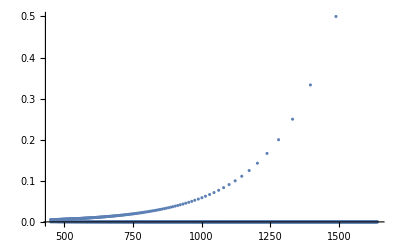

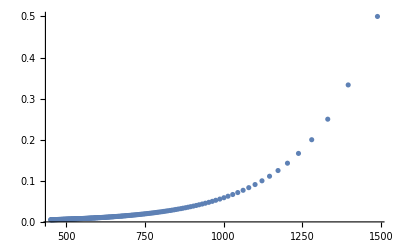

```mathematica
ListPlot[rrr]
ListPlot[rrrr,PlotRange->All]
```

```mathematica
NonlinearModelFit[rrrr,a+b*Exp[c*x+d],{a,b,c,d},x]
```

FittedModel[0.025539+105280. ⅇ^(-1.06653×10^6-203.967 x)]

```mathematica
gr=Table[{i,0.0},{i,3,1647}];
```

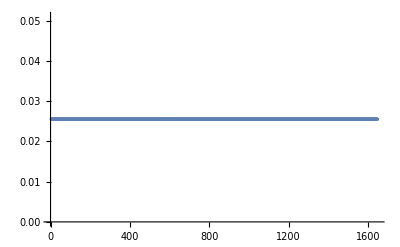

```mathematica
ListPlot[gr]
```

```mathematica
f[x_]:=Module[{y},{y=0.025538989458271596+105279.6407068865*Exp[-1.0665260356593165*10^6-203.96680427964236*x]}
]
```

```mathematica
f[100]
```

{0.025539}

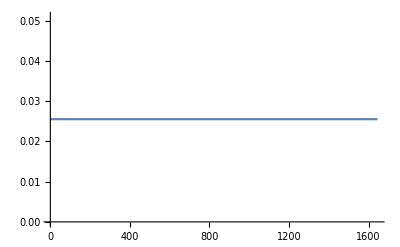

```mathematica
Plot[0.025538989458271596+105279.6407068865 ⅇ^(-1.0665260356593165*^6-203.96680427964236 x),{x,1,1645}]
```

```mathematica
xxx=11.08*0.028
```

0.31024

```mathematica
t1=xxx/0.045
```

6.89422

```mathematica
t2=xxx/0.37
```

0.838486

```mathematica
t3=xxx/0.082
```

3.78341

```mathematica
t4=11.08
```

11.08

```mathematica
t1+t2+t3+t4+t4
```

33.6761

```mathematica
75-37
```

38